```mathematica
Clear["Global`*"]
```

```mathematica
scaling=1;
a=scaling N[14/10];   (* == Carbon-Carbon Distance in A == *)
a0=√3 a ;(* == Lattice Constant Graphene == *)

(* == Direct Lattice == *)
a1=a0{1,0};  a2=a0{1/2,(√3)/2};                           (* == Direct Lattice Vectors == *)
kgr={0,0};  kpr=1/3*(2 a1-a2);                             (* == High symmetry points == *)
kmr=1/2(a1+a2);  kkr=1/3(a1-2 a2);

(* == Reciprocal Lattice == *)

{b1,b2}=2 π Inverse[Transpose[{a1,a2}]];  (* == Reciprocal Lattice Vectors == *)

b3=-( b1+b2);  
kg={0,0}; kp=1/3*(2 b1+b2);                             (* == High symmetry points == *)
km=1/2(b1+b2);  kk=1/3(b1+2 b2);


n=2600;(*Nk=3 n^2*) (* n = number of points that the mesh of the full 1BZ (with same Δk distance) would have*)
δn=80; (* δn = parameter analogous to n, but for the mini-kmesh*)
λ=(n-δn); (* λ is used when generating the meshes*)
Nq=2n; (*Nq = is the number of q points for which Π(q) will be calculated*)
{iqf,jqf}={0,n}; (*The indices of the vector pointing to the end of the q-path*)
(*In order to move in other direction, it might be convenient to project j along other kp vector*)

Npockets=2;
Vpocket=Table[0.,{i,1,Npockets}];
(*Defining where each pocket is centered at:*)
Vpocket[[1]]=-kp;

Vpocket[[2]]=-kk;
(*
Vpocket[[3]]=kp;
Vpocket[[4]]=0;
*)
(*This function transltes from indices i,j to vectors: *)
IndexToVector[kij_,k0_]:=Module[{sol},
sol=Table[kij[[i,j]].(1/n{kp,kk})+k0,{i,1,Length[kij]},{j,1,Length[kij[[i]]]}]
];

k0ij=Module[{sol},
sol=Table[{i,j},{i,-(n-λ)+1,(n-λ)},{j,Max[-(n-λ),-(n-λ)-i]+1,Min[(n-λ),(n-λ)-i]}]
];
k0pmesh=Table[IndexToVector[k0ij,Vpocket[[i]]],{i,1,Npockets}];

kqpathpij=Module[{sol},
sol=Table[{i,j},{i,-(n-λ)+1,(n-λ)},{j,Max[-(n-λ),-(n-λ)-i]+1-jqf,Min[(n-λ),(n-λ)-i]+jqf}]
];
kqpathpmesh=Table[IndexToVector[kqpathpij,Vpocket[[i]]],{i,1,Npockets}];
iq=Nq;
(*
kqij=Apply[{#1,#2-Nq+iq} &,k0ij,{2}];
*)
iq=n;
kqij=Apply[kqpathpij[[#1+(n-λ),#2+iq-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}];

kqpmesh=Table[IndexToVector[kqij,Vpocket[[i]]],{i,1,Npockets}];
```

```mathematica
(*Drawing the contours and vectors of the 1BZ for the figures: *)
BZcontour = Polygon[{((4π)/(3a0))*{-1,0},((4π)/(3a0))*{(-1)/2,(√3)/2},((4π)/(3a0))*{1/2,(√3)/2},((4π)/(3a0))*{1,0},((4π)/(3a0))*{1/2,(-√3)/2},((4π)/(3a0))*{(-1)/2,(-√3)/2}}];
ps=0.015;
BZvectors =Graphics[{
Red,Arrow[{{0,0},kk}],
Blue,Arrow[{{0,0},kp}],
Black,Arrow[{{0,0},b1}],
Black,Arrow[{{0,0},b2}],
Black, Text["b1",b1*1.05],
Black, Text["b2",b2*1.05],
Red, Text["K",kk*1.1],
Blue, Text["K'",kp*1.1],
Red,Opacity[0.1],EdgeForm [Dashed],
BZcontour
}];

(*Plotting the k mesh: *)

Show[
Graphics[{
PointSize[ps],
Green,
Table[Point[Flatten[k0pmesh[[i]],1]],{i,1,Npockets}]}],
BZvectors
]

ip=1;
ii=0;

Show[
Graphics[{
PointSize[ps],
Green,
Table[Point[Flatten[kqpathpmesh[[i]],1]],{i,1,Npockets}],
Purple,
Table[Point[Flatten[kqpmesh[[i]],1]],{i,1,Npockets}]
(*,
Red,
Point[Table[kqpathpmesh[[ip]][[ii+(n-λ),i-Max[-(n-λ),-(n-λ)-ii]]],{ii,-(n-λ)+1,(n-λ)}]]
*)
,
Red,
Point[Table[kqpathpmesh[[ip]][[ii+(n-λ),i-Max[-(n-λ),-(n-λ)-ii]]],{i,iq-δn+1+ 0.(-(n-λ)),iq+(n-λ)}]]

}],
BZvectors
]
```

```mathematica
(*a=2.46;a is given in units of 10^-10*)
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a0]*Exp[-ⅈ*ky*a0*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a0*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]];
```

```mathematica
μ=-0.052175;(* VHS is at μ=-0.052175;*)
kbT=0.0000861*1; (*Boltzmann's k × temperature*)
δc=10.*kbT; (*cutoff for the Fermi-Dirac distribution*)
FDif[ϵk_]=If[Abs[μ-ϵk]<δc,1/(1+Exp[(ϵk-μ)/kbT]),UnitStep[μ-ϵk]];
δFif[ϵk_]=If[Abs[μ-ϵk]<δc,-1./kbT/(2*(1+Cosh[(ϵk-μ)/kbT])),0.];
```

```mathematica
(*These arrays hold the same {i,j} structure than kij*)
Ekqpathpij=Table[Map[Eigenvalues,Apply[Hk,kqpathpmesh[[i]],{2}],{2}],{i,1,Npockets}];
ψkqpathpij=Table[Map[Eigenvectors,Apply[Hk,kqpathpmesh[[i]],{2}],{2}],{i,1,Npockets}];
nfEkqpathpij=Table[Map[FDif[#]&,Ekqpathpij[[i]],{3}],{i,1,Npockets}];

Ek=Flatten[Table[Flatten[Apply[Ekqpathpij[[i]][[#1+(n-λ),#2+n-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
ψk=Flatten[Table[Flatten[Apply[ψkqpathpij[[i]][[#1+(n-λ),#2+n-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
nfEk=Flatten[Table[Flatten[Apply[nfEkqpathpij[[i]][[#1+(n-λ),#2+n-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
```

```mathematica
i=0;
ip=1;
iq=1.Nq;


Epath=Table[
Flatten[Table[{(ii+iq+δn) Norm[kk/n],Ekqpathpij[[ip]][[i+(n-λ),ii+iq-Max[-(n-λ),-(n-λ)-i]]][[j]]},{ii,-(n-λ)+1-Nq, (n-λ)},{j,Nb}],1]
,{ip,1,Npockets}];

(*
Epath=Table[
Flatten[Table[{(ii+δn) Norm[kk/n],Ekqpathpij[[ip]][[i+(n-λ),ii-Max[-(n-λ),-(n-λ)-i]]][[j]]},{ii,iq-δn+1, (n-λ)+iq},{j,Nb}],1]
,{ip,1,Npockets}];
*)
K0=Norm[kk/n] Nq + 0. Vpocket[[1]][[1]] +0. Norm[Vpocket[[ip]]];
δK=1.2Norm[kk];
δE=1.5 γ0;
ListPlot[Epath,PlotRange->{{K0-δK,K0+δK},{-δE,δE}}]
```

```mathematica
qstep=Nq/10(*size of q-steps in units of Δk spacings*)
Δqij={0.,qstep};
Δq=Norm[Δqij.{kp/n,kk/n}];
Lq=Δq*Nq/qstep;
qi=Table[{(i qstep - Nq/2.) Δq,0.},{i,0,Nq/qstep}];
(*ERROR: why successive qi's are separated by Δq? shouldnt be Δq*qstep? *)
ω=0.;
```

520

{{0,0.0916418},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2600,0.267523},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{5200,0.0916477}}

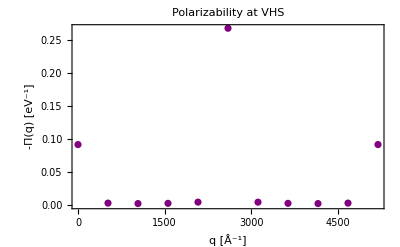

```mathematica
Πq0=Table[{0.,0.},{i,1,Nq/qstep+1}];
Monitor[

For[i=0,i≤Nq/qstep,i++,

q=i Δq;  (*Used for progress bar only*)

Ekq=Flatten[Table[Flatten[Apply[Ekqpathpij[[ip]][[#1+(n-λ),#2+i qstep-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
ψkq=Flatten[Table[Flatten[Apply[ψkqpathpij[[ip]][[#1+(n-λ),#2+i qstep-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
nfEkq=Flatten[Table[Flatten[Apply[nfEkqpathpij[[ip]][[#1+(n-λ),#2+i qstep-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];

Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Length[nfEk]}]];

ΔE=Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]]-Tuples[{Ek[[i]],Ekq[[i]]}][[All,2]],{i,Length[Ek]}]]+ω;

ψTuples=Table[Tuples[{ψk[[i]],ψkq[[i]]*}],{i,Length[Ek]}];


Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Length[Ek]},{j,Nb^2}]];


idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;

Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]],{i,Length[Ek]}]][[idiv]]];
Πq0[[i+1,1]]=i qstep;
Πq0[[i+1,2]]=-(2/(3 n^2))*Total[Δnf*Re[1/ΔE]*Fkq]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{0,1.1Δq Nq/qstep}],StringForm["``%",NumberForm[100*q/(Lq*1.05),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
Πq0
Show[ListPlot[Πq0, PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
```

{{0,11.8592},{130,367.461},{260,568.036},{520,1265.02},{1040,2353.48},{1560,517.125},{2080,286.142},{2340,195.534},{2470,3.92759},{2600,3.92538},{2730,197.543},{2860,290.064},{3120,525.652},{3640,2429.86},{4160,1250.67},{4680,564.26},{4940,364.98},{5070,11.8639}}

{65,2535,2665,5135}

{{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

{{65,0.0360103},{2535,0.0632625},{2665,0.063072},{5135,0.0360692}}

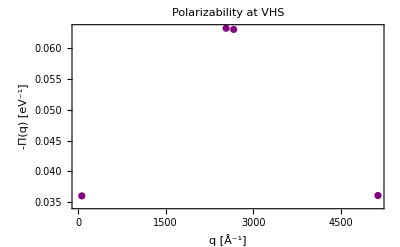

```mathematica
DΠ=Table[{Πq0[[i,1]],(Abs[Πq0[[i+1,2]]-Πq0[[i,2]]]+0.0001)^-1},{i,1,Length[Πq0]-1}]
NiMax=4 ;(*Must be smaller than initial number of points!*)
qstep=1/2 qstep;
iDmaxOrigi=Floor[Sort[DΠ[[Ordering[DΠ[[All,2]]],1]][[1;;NiMax]]]+qstep]

Πq02=Table[{0.,0.},{i,1,NiMax}]

Monitor[

For[i=1,i≤NiMax,i++,

q=i Δq;  (*Used for progress bar only*)

Ekq=Flatten[Table[Flatten[Apply[Ekqpathpij[[ip]][[#1+(n-λ),#2+iDmaxOrigi[[i]] -Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
ψkq=Flatten[Table[Flatten[Apply[ψkqpathpij[[ip]][[#1+(n-λ),#2+iDmaxOrigi[[i]]-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
nfEkq=Flatten[Table[Flatten[Apply[nfEkqpathpij[[ip]][[#1+(n-λ),#2+iDmaxOrigi[[i]]-Max[-(n-λ),-(n-λ)-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];

Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Length[nfEk]}]];

ΔE=Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]]-Tuples[{Ek[[i]],Ekq[[i]]}][[All,2]],{i,Length[Ek]}]]+ω;

ψTuples=Table[Tuples[{ψk[[i]],ψkq[[i]]*}],{i,Length[Ek]}];


Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Length[Ek]},{j,Nb^2}]];


idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;

Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]],{i,Length[Ek]}]][[idiv]]];
Πq02[[i,1]]=iDmaxOrigi[[i]];
Πq02[[i,2]]=-(2/(3 n^2))*Total[Δnf*Re[1/ΔE]*Fkq]
]
,Grid[{{Text[Style["Progress:",Darker[Blue,0.66]]],ProgressIndicator[q,{Δq,(NiMax+1) Δq}],StringForm["``%",NumberForm[100*q/(Lq*1.05),{3,2}]]},{Text[Style["Current value of q: ",Darker[Blue,0.66]]],q ,StringForm["Final value: ``",NumberForm[Lq]] }},Alignment->Left,Dividers->Center]];
Πq02
Show[ListPlot[Πq02, PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, FrameLabel->{"q [Å^-1]",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
```

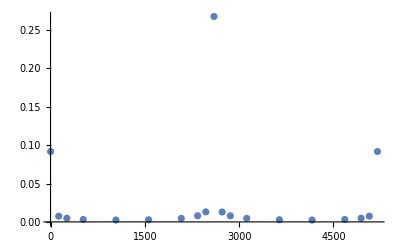

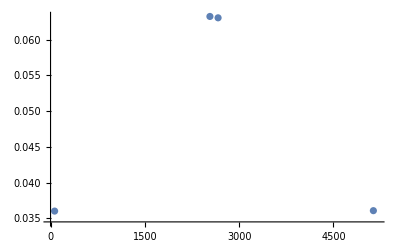

{{0,0.0916418},{130,0.00741892},{260,0.00479754},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2340,0.00800003},{2470,0.0130142},{2600,0.267523},{2730,0.0128703},{2860,0.00790812},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{4940,0.00481847},{5070,0.00745834},{5200,0.0916477}}

{{65,0.0360103},{2535,0.0632625},{2665,0.063072},{5135,0.0360692}}

{{0,0.0916418},{65,0.0360103},{130,0.00741892},{260,0.00479754},{520,0.00313709},{1040,0.00244659},{1560,0.00277149},{2080,0.00460526},{2340,0.00800003},{2470,0.0130142},{2535,0.0632625},{2600,0.267523},{2665,0.063072},{2730,0.0128703},{2860,0.00790812},{3120,0.00456061},{3640,0.00275821},{4160,0.00244667},{4680,0.00314624},{4940,0.00481847},{5070,0.00745834},{5135,0.0360692},{5200,0.0916477}}

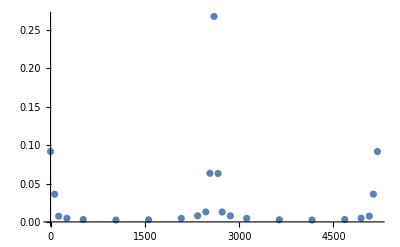

```mathematica
Show[ListPlot[{Πq0},PlotRange->{{0,5200},All}]]
Show[ListPlot[{Πq02},PlotRange->{{0,5200},All}]]
Π1p2=Join[Πq0,Πq02];
Ordering[Π1p2[[All,1]]];
Πq0
Πq02
Πq0=Π1p2[[Ordering[Π1p2[[All,1]]]]]
ListPlot[Πq0,PlotRange->All]
```